## Task1 : Elastic bar problem

```mathematica
(* Given information *)
```

```mathematica
l=3;EA=1;K=10;
C4=4 2; 
force=1/2;
p[x_]:=1+Sin[Pi x]/2;
```

#### 1.1 Set up a, b, energy funcional

```mathematica
F[u_,v_,ud_,vd_]:=EA ud vd + C4 u v
```

```mathematica
a[u_,v_]:=Integrate[F[u,v,D[u,x],D[v,x]],{x,0,l}] + K (u/.x->l) (v/.x->l)
```

```mathematica
b[v_]:=Integrate[v p[x],{x,0,l}] + force (v/.x->l)
```

```mathematica
phi[u_]:=a[u,u]/2 -b[u]
```

```mathematica
ClearAttributes[phin,Protected];
Clear[phin];
phin[u_]:=Module[{a,b},
a=NIntegrate[F[u,u,D[u,x],D[u,x]],{x,0,l}] + K (u/.x->l) (u/.x->l);
b=NIntegrate[u p[x],{x,0,l}] + force (u/.x->l);
a/2 -b]
SetAttributes[phin,{Protected}];
```

#### 1.2 Create two kinds of basis functions

```mathematica
n=10;
```

```mathematica
(* basis-p suitable polynomials *)
```

```mathematica
basisP[n_]:=Table[x^i,{i,1,n}]
```

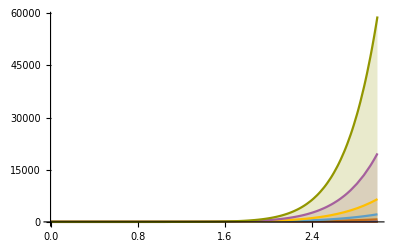

```mathematica
Plot[Evaluate[Table[basisP[i][[i]],{i,1,n}]],{x,0,3},PlotRange->All,Filling->Axis]
```

```mathematica
(* piecewise linear finite element basis *)
```

```mathematica
basisF[n_]:=Module[{h},
h=l/n;
triFunc=Function[x,
Table[
Piecewise[
{
{0,x<i h-h},
{(x-(i h-h))/h,x<i h},
{1-(x-i h)/h,x<i h+h},
{0,True}
}
],{i,1,n}]][x];
Return[triFunc];]
```

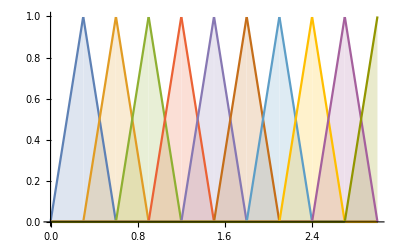

```mathematica
Plot[Evaluate[Table[basisF[n][[i]],{i,1,n}]],{x,0,3},PlotRange->All,Filling->Axis]
```

#### 1.3 Set up a function computing he approximation

#### 1.4 Compute and plot for 2 types

```mathematica
un[basis_]:=Module[{n,stiffMa,rhsMa,uh},
n=Dimensions[basis][[1]];
stiffMa=Table[a[basis[[i]],basis[[j]]],{i,1,n},{j,1,n}];
rhsMa=Table[b[basis[[i]]],{i,1,n}];
uh=LinearSolve[stiffMa,rhsMa];
uh.basis//Simplify//N
]
```

```mathematica
(* Polynomail basis *)
```

```mathematica
unP=Table[un[basisP[i]],{i,1,n}];
```

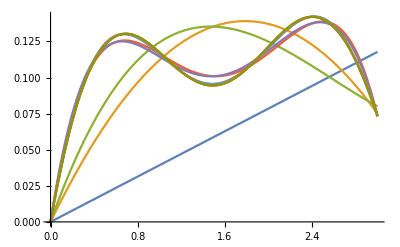

```mathematica
Plot[unP,{x,0,3}]
```

```mathematica
(* Piecewise basis *)
```

```mathematica
unF=Table[un[basisF[i]],{i,1,n}];
```

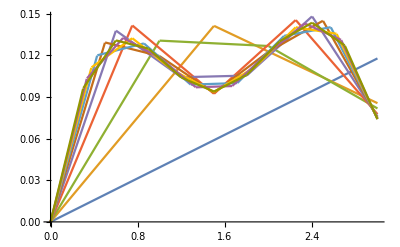

```mathematica
Plot[unF,{x,0,3}]
```

#### 1.5 Show basis functions decreasing

```mathematica
(* Polynomial basis *)
```

```mathematica
enP=Table[phi[unP[[i]]],{i,1,Length[unP]}];
enPn=Table[phin[unP[[i]]],{i,1,Length[unP]}];
```

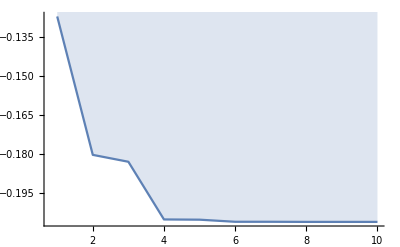

-Graphics-

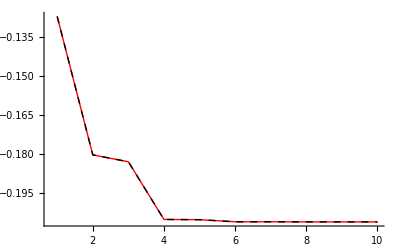

```mathematica
ListPlot[enP,Filling->Axis,Joined->True,PlotRange->Full]
ListPlot[enPn,Filling->Axis,Joined->True,PlotRange->Full]
ListPlot[{enP,enPn},Joined->True,PlotRange->Full,PlotStyle->{Directive[Red,Thick],Directive[Black,Thin,Dashed]}]
```

```mathematica
(* Piecewise basis *)
```

```mathematica
enF=Table[phi[unF[[i]]],{i,1,Length[unP]}];
enFn=Table[phin[unF[[i]]],{i,1,Length[unP]}];
```

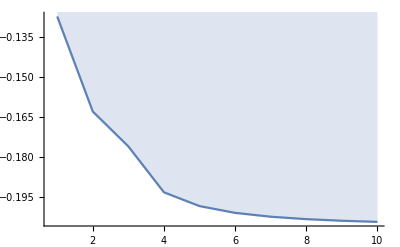

-Graphics-

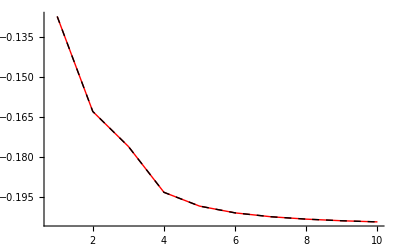

```mathematica
ListPlot[enF,Filling->Axis,Joined->True,PlotRange->Full]
ListPlot[enFn,Filling->Axis,Joined->True,PlotRange->Full]
ListPlot[{enF,enFn},Joined->True,PlotRange->Full,PlotStyle->{Directive[Red,Thick],Directive[Black,Thin,Dashed]}]
```

```mathematica
(* Comparison *)
```

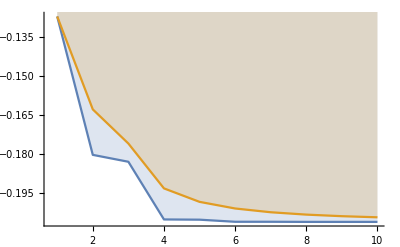

```mathematica
ListPlot[{enPn,enFn},Filling->Axis,PlotRange->All,Joined->True,PlotRange->All]
```